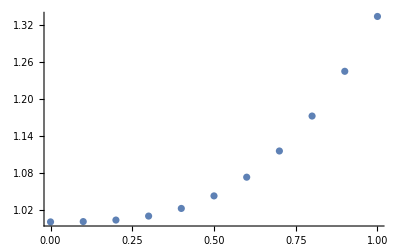

```mathematica
Clear[y]
f[x_,y_]:=x*Sin[x*y]
y[0]=1;
h:=0.1;
Do[k1=h f[h n,y[n]];
k2=h f[h (n+1),y[n]+k1];
y[n+1]=y[n]+.5 (k1+k2),{n,0,10}]
a=ListPlot[Table[{n*h,y[n]},{n,0,10}]]
```

```mathematica
y[10]
```

1.33341

```mathematica
Clear[y];
```

```mathematica
s=NDSolve[{y'[x]==x*Sin[x*y[x]],y[0]==1},y,{x,0,1}]
```

{{y→InterpolatingFunction[{{0., 1.}}, <>]}}

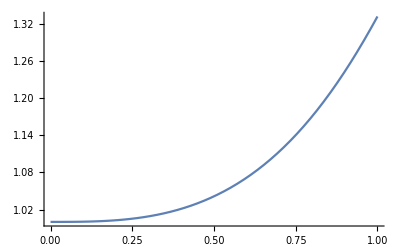

```mathematica
b=Plot[Evaluate[y[x]/.s],{x,0,1},PlotRange->All]
```

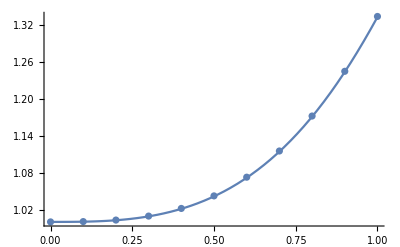

```mathematica
Show[a,b]
```